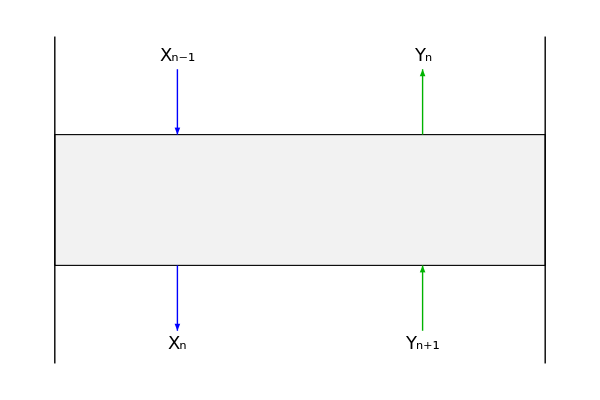

```mathematica
Module[{colL,colV,δx,δy,δw,δh,th1,th2},
colL=Blue;colV=RGBColor[0,0.7,0];
δx=1;δy=0.4*δx;δw=0.35*δx;δh=0.5*δy;
th1=0.015;th2=0.007;

Graphics[{
{EdgeForm@Thick,FaceForm@GrayLevel@0.95,Rectangle[{0,0},{δx,δy}]},
Thick,Line[{{#,-0.75*δy},{#,1.75*δy}}]&/@{0,δx},
Arrowheads@0.07,
{Blue,Arrow[{{0.25*δx,δy+δh},{0.25*δx,δy}}],Arrow[{{0.25*δx,0},{0.25*δx,-δh}}]},
{RGBColor[0,0.7,0],Arrow[{{0.75*δx,δy},{0.75*δx,δy+δh}}],Arrow[{{0.75*δx,-δh},{0.75*δx,0}}]},
Text[Style[Subscript[Style["X",Italic],#1],18],{0.25*δx,#2}]&@@@{{"n-1",δy+1.2*δh},{"n",-1.2*δh}},
Text[Style[Subscript[Style["Y",Italic],#1],18],{0.75*δx,#2}]&@@@{{"n",δy+1.2*δh},{"n+1",-1.2*δh}}
},ImageSize->{600,400}]
]
```

```mathematica
Manipulate[
Module[{Ea,R,H0,HB,ρ,MW,μ,X0,Y1,XN,Yeq,YN1,Yinlet,sol,check,check2,stage,test,n,steps,stepping,KN,E0},
Ea=5000;R=8.314;
H0=Hi/.Solve[211.19==Hi*Exp[-5000/8.314/298],Hi][[1]];
HB=H0*Exp[-Ea/(R*(T+273))];

ρ=94.27;(*lb/ft3*)MW=63.01;(*g/mol*)
μ=Quiet@Interpolation[{{0,3.5},{20,2.5},{50,1.4},{100,0.7}}][T];(*cP*)

X0=0;Y1=10;XN=1.3;
Yeq[x_]:=HB/P*x;
YN1[x_]:=LV*(x-X0)+Y1;
Yinlet[x_]:=yn1;

sol=x/.Solve[Yeq[x]==Yinlet[x],x][[1]];
check=x/.Solve[YN1[x]==Yinlet[x],x][[1]];
check2=x/.Solve[Yeq[x]==YN1[x],x][[1]];
stage[1]=x/.Solve[Yeq[x]==Y1,x][[1]];

Do[stage[i]=x/.Solve[Yeq[x]==YN1[stage[i-1]],x][[1]],{i,2,50}];

test=Table[stage[n],{n,1,50}];

n=1;While[test[[n]]<check∧If[check2>0,Yeq[check2]>Yinlet[check2],True],n++];

steps=Flatten[Table[{
{test[[i]],Yeq[test[[i]]]},
{test[[i]],YN1[test[[i]]]}},
{i,1,n}],1];

stepping=ReplacePart[Join[{{0,Y1}},steps],{2*n+1,2}->yn1];

KN=YN1[n]/(1+YN1[n])/(XN/(1+XN));
E0=10^(1.597-0.199*Log10[(KN*MW*μ)/ρ]-0.0896*Log10[(KN*MW*μ)/ρ]^2);

Plot[{Yeq[x],YN1[x],Yinlet[x]},{x,0,XN},PlotStyle->{{Thick,Blue},{Thick,Black},{Thick,Dashed,RGBColor[0,0.6,0]}},
Frame->True,FrameLabel->{Row@{Style["X",Italic]," (ppm)"},Row@{Style["Y",Italic]," (ppm)"}},LabelStyle->{17,Black},ImageSize->600,PlotLabel->{YN1[n]/(1+YN1[n])/(XN/(1+XN)),Yeq[n]/(1+Yeq[n])/(XN/(1+XN)),n},
Epilog->{
Line[stepping],Text[Style[#,16],{stage[#]+0.025,Yeq[stage[#]]-3}]&/@Range@n
}];E0
],
Grid[{
{Control[{{P,2.5,"pressure (atm)"},1.5,3,0.1,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft,
Control[{{T,25,"Temperature °C"},10,80,5,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft},
{Control[{{LV,100,Row@{Style["L",Italic],"/",Style["V",Italic]}},50,300,5,Appearance->"Labeled"(*,ImageSize->Small*)}],SpanFromLeft,
Control[{{yn1,100,"inlet concentration (ppm)"},40,120,1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left]
]
```

```mathematica
Manipulate[
Module[{Ea,R,H0,HB,ρ,MW,μ,X0,Y1,yn1,Yeq,YN1,Yinlet,sol,check,check2,stage,test,n,KN,E0,XN},
Ea=5000;R=8.314;
H0=Hi/.Solve[211.19==Hi*Exp[-5000/8.314/298],Hi][[1]];
HB=H0*Exp[-Ea/(R*(T+273))];

ρ=94.27;(*lb/ft3*)MW=63.01;(*g/mol*)
μ=Quiet@Interpolation[{{0,3.5},{20,2.5},{50,1.4},{100,0.7}}][T];(*cP*)

X0=0;Y1=10;yn1=100;
Yeq[x_]:=HB/P*x;
YN1[x_]:=LV*(x-X0)+Y1;
Yinlet[x_]:=yn1;

sol=x/.Solve[Yeq[x]==Yinlet[x],x][[1]];
check=x/.Solve[YN1[x]==Yinlet[x],x][[1]];
check2=x/.Solve[Yeq[x]==YN1[x],x][[1]];
stage[1]=x/.Solve[Yeq[x]==Y1,x][[1]];

Do[stage[i]=x/.Solve[Yeq[x]==YN1[stage[i-1]],x][[1]],{i,2,50}];

test=Table[stage[n],{n,1,50}];

n=1;While[test[[n]]<check∧If[check2>0,Yeq[check2]>Yinlet[check2],True],n++];

KN=YN1[n]/(1+YN1[n])/(xn/(1+xn));
E0=10^(1.597-0.199*Log10[(KN*MW*μ)/ρ]-0.0896*Log10[(KN*MW*μ)/ρ]^2);
XN=xn/.FindRoot[E0==e0,{xn,0.1}]
],
Grid[{
{Control[{{P,2.5,"pressure (atm)"},1.5,3,0.1,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft,
Control[{{T,25,"Temperature °C"},10,80,5,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft},
{Control[{{LV,100,Row@{Style["L",Italic],"/",Style["V",Italic]}},50,300,5,Appearance->"Labeled"(*,ImageSize->Small*)}],SpanFromLeft,
Control[{{e0,31,"efficiency"},10,35,1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left]
]
```

```mathematica
Manipulate[
Module[{P,T,LV,Ea,R,H0,HB,ρ,MW,μ,X0,Y1,yn1,Yeq,YN1,Yinlet,sol,check,check2,stage,test,n,KN,E0,XN},
P=2.5;T=25;LV=100;

Ea=5000;R=8.314;
H0=Hi/.Solve[211.19==Hi*Exp[-5000/8.314/298],Hi][[1]];
HB=H0*Exp[-Ea/(R*(T+273))];

ρ=94.27;(*lb/ft3*)MW=63.01;(*g/mol*)
μ=Quiet@Interpolation[{{0,3.5},{20,2.5},{50,1.4},{100,0.7}}][T];(*cP*)

X0=0;Y1=10;yn1=100;
Yeq[x_]:=HB/P*x;
YN1[x_]:=LV*(x-X0)+Y1;
Yinlet[x_]:=yn1;

sol=x/.Solve[Yeq[x]==Yinlet[x],x][[1]];
check=x/.Solve[YN1[x]==Yinlet[x],x][[1]];
check2=x/.Solve[Yeq[x]==YN1[x],x][[1]];
stage[1]=x/.Solve[Yeq[x]==Y1,x][[1]];

Do[stage[i]=x/.Solve[Yeq[x]==YN1[stage[i-1]],x][[1]],{i,2,50}];

test=Table[stage[n],{n,1,50}];

n=1;While[test[[n]]<check∧If[check2>0,Yeq[check2]>Yinlet[check2],True],n++];

KN=YN1[n]/(1+YN1[n])/(xn/(1+xn));
E0=10^(1.597-0.199*Log10[(KN*MW*μ)/ρ]-0.0896*Log10[(KN*MW*μ)/ρ]^2);
XN=xn/.FindRoot[E0==e0,{xn,0.1}]
],
Control[{{e0,31,"efficiency"},10,35,1,Appearance->"Labeled"}]
]
```